```mathematica
(*Define constants of the problem*)
kBT=1.380649*10^(-23) * 200 * 10^-9;
a0=5.29*10^(-11);
hPlanck=6.62607015*10^(-34);
hbar=hPlanck/(2*Pi);
muNa40K=14.594251717637002*1.660538782*10^(-27);
ai=-2831.85 * a0;
af=9.82 * a0;
(*energies in units of kBT*)
Ei=hbar^2/(2*muNa40K*ai^2) / kBT;
Ef=hbar^2/(2*muNa40K*af^2) / kBT;
```

```mathematica
(*Lineshape from first-order calculation*)
```

```mathematica
Lineshape[rf_,Ek_]:=(Sqrt[Ek]/(1+Ek/Ei))*(1/(1+(rf+Ek)/Ef))*(Sqrt[rf+Ek]/(rf^2))*(ai-af)^2
```

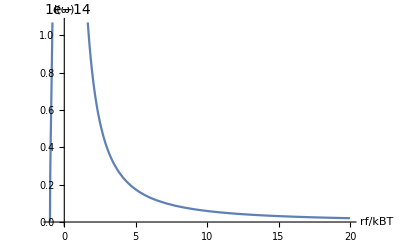

```mathematica
Plot[Lineshape[rf,1],{rf,-10,20},PlotRange->Automatic, AxesLabel->{"rf/kBT","I(ω)"}]
```

```mathematica
ConvolvedLineshape[rf_]:=NIntegrate[Lineshape[rf,Ek]*Exp[-Ek],{Ek,0,2}];
```

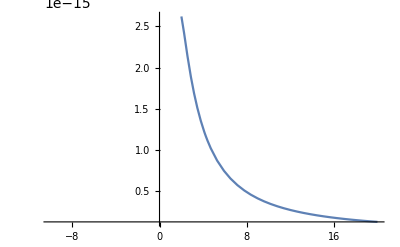

```mathematica
Plot[ConvolvedLineshape[rf],{rf,-10,20},PlotRange->Full]
```

```mathematica
(1/(2*Pi))*(h*OR^2)*Integrate[Sqrt[e*EM]/((e+EM)^2*e*(En-e)),{e,0,Infinity},PrincipalValue->True]
```

ConditionalExpression[((3 EM+En) h OR^2)/(4 EM (EM+En)^2), Im[En]==0&&(Im[EM]≠0||Re[EM]≥0)&&Re[En]>0]

```mathematica
(*Threshold function convolved with Blackman envelope*)
```

```mathematica
Thres[rf_,Eb_]:=Sqrt[rf-Eb]/rf^2;
```

```mathematica
ConvoledDissociationLine[rf_]:=NIntegrate[Thres[rf,Eb]*PDF[NormalDistribution[100,10],Eb],{Eb,-100,100}]
```

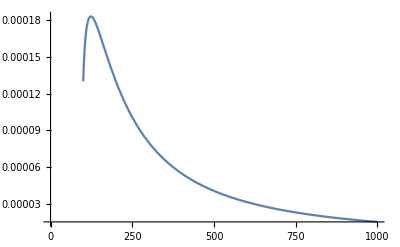

```mathematica
Plot[ConvoledDissociationLine[rf],{rf,0,1000},PlotRange->Full]
```

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
A[w_]:=NIntegrate[k*Exp[-k^2/2]*k/((w - k^2)^2 + 0.5*k^2),{k,0,1000}]
```

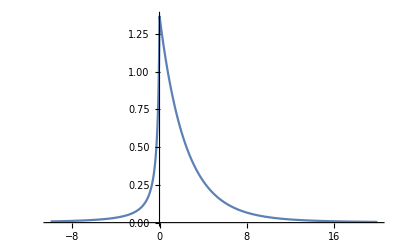

```mathematica
Plot[A[w],{w,-10,20},PlotRange->Full]
```

```mathematica
FullSimplify[Abs[(x1-I*y1)*(x2-I*y2)-a]^2,Assumptions->{x1>0,y1>0,x2>0,y2>0,a>0}]
```

(x2 y1+x1 y2)^2+(a-x1 x2+y1 y2)^2

```mathematica
FullSimplify[Abs[a+I*b]^2,Assumptions->{a>0,b>0}]
```

a^2+b^2

```mathematica
FullSimplify[Im[1/(a+I*b)],Assumptions->{a>0,b>0}]
```

Im[1/(a+ⅈ b)]

```mathematica
G[w_]:=1/(w-Ep-I*Su - Ω0^2/4 * 1/(w - Ep - Δ0-I*Sd));
```

```mathematica
ComplexExpand[1/(a-I*b)]
```

a/(a^2+b^2)+(ⅈ b)/(a^2+b^2)

```mathematica
Transmission[x_]:=1-0.8*20^2/(x^2+20^2)+0.03/((x-15)^2+0.75^2)+0.05/((x+20)^2+0.75^2)-0.15/((x+1)^2+1^2);
```

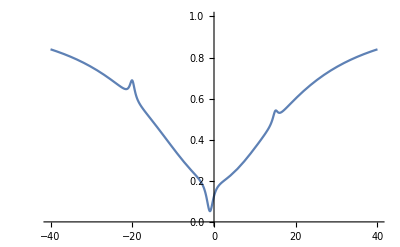

```mathematica
Plot[Transmission[x],{x,-40,40},PlotRange->{0,1}]
```

```mathematica
D[Transmission[x],x]
```

-(0.06 (-15+x))/((0.5625+(-15+x)^2)^2)+(640. x)/((400+x^2)^2)+(0.3 (1+x))/((1+(1+x)^2)^2)-(0.1 (20+x))/((0.5625+(20+x)^2)^2)

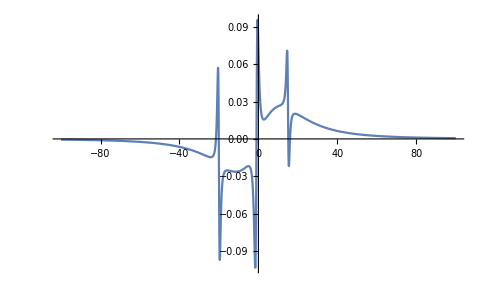

```mathematica
Plot[-(0.06 (-15+x))/((0.5625+(-15+x)^2)^2)+(640. x)/((400+x^2)^2)+(0.3 (1+x))/((1+(1+x)^2)^2)-(0.1 (20+x))/((0.5625+(20+x)^2)^2),{x,-100,100},PlotRange->Full]
```

```mathematica
pCOM=pNa+pK;
mu=mNa*mK/(mNa+mK);
pRel=(pNa/mNa-pK/mK)*mu;
mTot=mNa+mK;
```

```mathematica
pCOM^2/(2(mNa+mK))+pRel^2/(2*mu)//FullSimplify
```

1/2 (pK^2/mK+pNa^2/mNa)

```mathematica
Exp[-(ek-m)*t]*(-1+1/(Exp[b*(ek-m)]))//FullSimplify
```

ⅇ^((-ek+m) t) (-1+ⅇ^(b (-ek+m)))

```mathematica
f[w_]=(4*Pi/(2m))*1/(1/3-Sqrt[-2*m*w]);
```

```mathematica
InverseLaplaceTransform[f[w],w,t]
```

-(2 π (-1/6 ⅇ^(-t/(18 m))-(√(-m/t))/(√(2 π))+(ⅇ^(-t/(18 m)) m^(3/2) (-t/m)^(3/2) Erfi[(√t)/(3 √2 √m)])/(6 t^(3/2))))/m^2

```mathematica
n[z]:=1/(Exp[bEk]/z-1);
```

```mathematica
Series[n[z],{z,0,4}]
```

ⅇ^-bEk z+ⅇ^(-2 bEk) z^2+ⅇ^(-3 bEk) z^3+ⅇ^(-4 bEk) z^4+O[z]^5

```mathematica
ComplexExpand[Sqrt[x+I*t]]
```

(t^2+x^2)^(1/4) Cos[1/2 Arg[ⅈ t+x]]+ⅈ (t^2+x^2)^(1/4) Sin[1/2 Arg[ⅈ t+x]]

```mathematica
Limit[Im[a]/((Im[a]^2+Re[a]^2) ((Re[a]/(Im[a]^2+Re[a]^2)-√2 Cos[1/2 Arg[-m (ⅈ p+w)]] √(√(Im[m]^2+Re[m]^2) √((Im[w]+Re[p])^2+(-Im[p]+Re[w])^2)))^2+(-Im[a]/(Im[a]^2+Re[a]^2)-√2 √(√(Im[m]^2+Re[m]^2) √((Im[w]+Re[p])^2+(-Im[p]+Re[w])^2)) Sin[1/2 Arg[-m (ⅈ p+w)]])^2))+(√2 √(√(Im[m]^2+Re[m]^2) √((Im[w]+Re[p])^2+(-Im[p]+Re[w])^2)) Sin[1/2 Arg[-m (ⅈ p+w)]])/((Re[a]/(Im[a]^2+Re[a]^2)-√2 Cos[1/2 Arg[-m (ⅈ p+w)]] √(√(Im[m]^2+Re[m]^2) √((Im[w]+Re[p])^2+(-Im[p]+Re[w])^2)))^2+(-Im[a]/(Im[a]^2+Re[a]^2)-√2 √(√(Im[m]^2+Re[m]^2) √((Im[w]+Re[p])^2+(-Im[p]+Re[w])^2)) Sin[1/2 Arg[-m (ⅈ p+w)]])^2),p->0]
```

ConditionalExpression[Im[a]/((Im[a]^2+Re[a]^2) ((Re[a]/(Im[a]^2+Re[a]^2)-√2 Cos[1/2 Arg[-m w]] √(√(Im[m]^2+Re[m]^2) √(Im[w]^2+Re[w]^2)))^2+(-Im[a]/(Im[a]^2+Re[a]^2)-√2 √(√(Im[m]^2+Re[m]^2) √(Im[w]^2+Re[w]^2)) Sin[1/2 Arg[-m w]])^2))+(√2 √(√(Im[m]^2+Re[m]^2) √(Im[w]^2+Re[w]^2)) Sin[1/2 Arg[-m w]])/((Re[a]/(Im[a]^2+Re[a]^2)-√2 Cos[1/2 Arg[-m w]] √(√(Im[m]^2+Re[m]^2) √(Im[w]^2+Re[w]^2)))^2+(-Im[a]/(Im[a]^2+Re[a]^2)-√2 √(√(Im[m]^2+Re[m]^2) √(Im[w]^2+Re[w]^2)) Sin[1/2 Arg[-m w]])^2), √(Im[m]^2+Re[m]^2)>0&&Im[w]^2+Re[w]^2>0]

```mathematica
Series[Sqrt[x+I*t],{t,0,3}]
```

√x+(ⅈ t)/(2 √x)+t^2/(8 x^(3/2))-(ⅈ t^3)/(16 x^(5/2))+O[t]^4

```mathematica
ComplexExpand[1/(1/2-Sqrt[-(x+I/1000)])]
```

1/(2 ((1/2-(1/1000000+x^2)^(1/4) Cos[1/2 Arg[-ⅈ/1000-x]])^2+√(1/1000000+x^2) Sin[1/2 Arg[-ⅈ/1000-x]]^2))-((1/1000000+x^2)^(1/4) Cos[1/2 Arg[-ⅈ/1000-x]])/((1/2-(1/1000000+x^2)^(1/4) Cos[1/2 Arg[-ⅈ/1000-x]])^2+√(1/1000000+x^2) Sin[1/2 Arg[-ⅈ/1000-x]]^2)+(ⅈ (1/1000000+x^2)^(1/4) Sin[1/2 Arg[-ⅈ/1000-x]])/((1/2-(1/1000000+x^2)^(1/4) Cos[1/2 Arg[-ⅈ/1000-x]])^2+√(1/1000000+x^2) Sin[1/2 Arg[-ⅈ/1000-x]]^2)

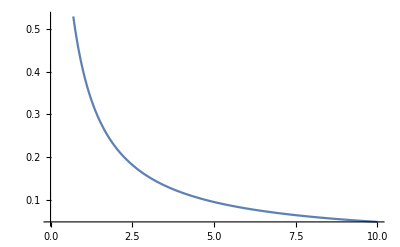

```mathematica
Plot[1/(2 ((1/2)^2+√(1/1000000+x^2))),{x,0,10}]
```

```mathematica
N[Cos[1/2 Arg[-ⅈ/100-0]]]
```

0.707107

```mathematica
N[Arg[1]]
```

0.

```mathematica
ComplexExpand[(4*Pi/(2*m))*1/(1/a-Sqrt[-2*m*(x+I*t)])]
```

(2 π)/(a m ((1/a-√2 (m^2 t^2+m^2 x^2)^(1/4) Cos[1/2 Arg[-m (ⅈ t+x)]])^2+2 √(m^2 t^2+m^2 x^2) Sin[1/2 Arg[-m (ⅈ t+x)]]^2))-(2 √2 π (m^2 t^2+m^2 x^2)^(1/4) Cos[1/2 Arg[-m (ⅈ t+x)]])/(m ((1/a-√2 (m^2 t^2+m^2 x^2)^(1/4) Cos[1/2 Arg[-m (ⅈ t+x)]])^2+2 √(m^2 t^2+m^2 x^2) Sin[1/2 Arg[-m (ⅈ t+x)]]^2))+(2 ⅈ √2 π (m^2 t^2+m^2 x^2)^(1/4) Sin[1/2 Arg[-m (ⅈ t+x)]])/(m ((1/a-√2 (m^2 t^2+m^2 x^2)^(1/4) Cos[1/2 Arg[-m (ⅈ t+x)]])^2+2 √(m^2 t^2+m^2 x^2) Sin[1/2 Arg[-m (ⅈ t+x)]]^2))

```mathematica
(2 π)/(a m ((1/a)^2+2 *m*x ))//FullSimplify
```

(2 a π)/(m+2 a^2 m^2 x)

```mathematica
(1/Pi)*(2Sqrt[2]/m^(3/2))*Integrate[Sqrt[x]/((x+1/(2*m*a^2))*(x-y)),{x,-Infinity,Infinity},PrincipalValue->True]
```

ConditionalExpression[(4 √2 a^2 ((√2 π)/(√m)-2 π √-y Abs[a]))/(√m π (2 Abs[a]+4 a^2 m y Abs[a])), 1/a^2∈ℝ&&y<0&&m>0&&a^2 m y>-1/2]

```mathematica
(4 √2 a ((√2 π)/(√m)-2 π √-y a))/(√m π (2+4 a^2 m y ))//FullSimplify
```

(4 a)/(m+√2 a m^(3/2) √-y)

```mathematica
(*En=1, mNa=1,mK=1, Eb=0.1*)
```

```mathematica
F[k_]:=N[Integrate[x^2*Exp[-(x)^2/2]*Sqrt[1-x^2/4+(x-k)^2/2]/(1-x^2/4+(x-k)^2/2+0.1),{x,0,100}]]
```

```mathematica
Plot[F[k],{k,0,1}]
```

$Aborted

```mathematica
z=0.1;
```

```mathematica
RePart=N[Integrate[q^2*8*Pi/(1 + q^2),{q,0,100}]];
```

```mathematica
ImPart=N[Integrate[(q^3/2)*8*Pi/(1 + q^2),{q,0,100}]];
```

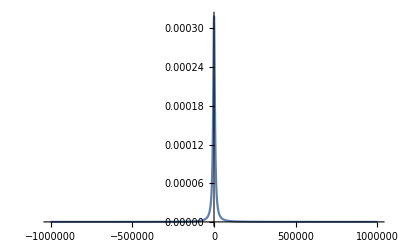

```mathematica
Plot[2*z*ImPart/((d-z*RePart)^2+(z*ImPart)^2),{d,-1000000,1000000},PlotRange->Full]
```

```mathematica
F[En_]:=N[Integrate[P^2*Exp[-P^2]/(1 - Sqrt[-En - P^2/4]),{P,0,10}]]
```

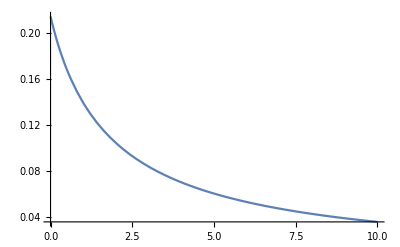

```mathematica
Plot[Re[F[En]],{En,0,10}]
```

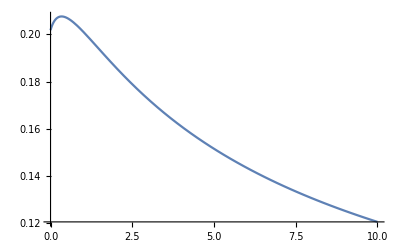

```mathematica
Plot[Im[F[En]],{En,0,10}]
```